```mathematica
<<ToMatlab.m;
```

```mathematica
G = Sqrt[Exp[2 t]-1];
```

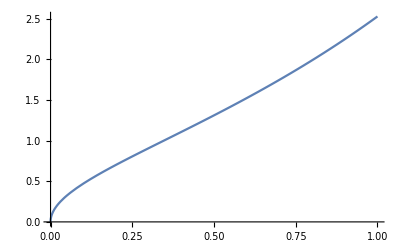

```mathematica
Plot[G,{t,0,1}]
```

```mathematica
P = G/2 Exp[-(G^2-1)InverseErf[ϕ]^2];
```

```mathematica
Integrate[P/.{t->1},{ϕ,-1,1}]
```

1

```mathematica
ToMatlab[P]
```

(1/2).*exp(1).^((2+(-1).*exp(1).^(2.*t)).*InverseErf(ϕ).^2).*((-1) ...
  +exp(1).^(2.*t)).^(1/2);

```mathematica
Plot3D[P,{t,0.1,1},{ϕ,-0.95,0.95},AxesLabel->{t,ϕ}]
```

-Graphics3D-

```mathematica
σ = √(2/Pi ArcTan[1/(G √(G^2+2))]);
```

```mathematica
ϵ = - σ D[σ,t]//FullSimplify;
```

```mathematica
δ = ϵ((-√Pi)/Sin[Pi/2 σ^2] √((1 + Sin[Pi/2 σ^2])/(1 - Sin[Pi/2 σ^2])))Exp[-InverseErf[ϕ]^2]InverseErf[ϕ]//FullSimplify;
```

```mathematica
ToMatlab[δ]
```

(-1).*exp(1).^((-1).*InverseErf(ϕ).^2).*pi.^(-1/2).*InverseErf(ϕ) ...
  .*(2+coth(t)+tanh(t)).^(1/2).*((-1).*((-2).*cosh(4.*t)+(-2).*sinh( ...
  4.*t)+((-1)+exp(1).^(2.*t)).^(1/2).*(1+exp(1).^(2.*t)).^(1/2).*(2+ ...
  coth(t)+tanh(t)).^(1/2)).^(-1).*(2.*cosh(4.*t)+2.*sinh(4.*t)+((-1) ...
  +exp(1).^(2.*t)).^(1/2).*(1+exp(1).^(2.*t)).^(1/2).*(2+coth(t)+ ...
  tanh(t)).^(1/2))).^(1/2);

```mathematica
Plot3D[δ ,{t,0.1,1},{ϕ,-.95,.95},AxesLabel->{t,ϕ}]
```

-Graphics3D-

```mathematica
res = D[P,t]+D[δ  P,ϕ]//FullSimplify;
```

```mathematica
Plot3D[res,{t,0.1,1},{ϕ,-0.95,.95},AxesLabel->{t,ϕ}]
```

-Graphics3D-